```mathematica
Directory[]
```

/home/mrudolph/Desktop/Spektro

```mathematica
data:=Import["1000.dat","Table"]
```

```mathematica
model={a1 Exp[-b1 (x-x1)^2] 
+ a2 Exp[-b2 (x-x2)^2] 
+ a3 Exp[-b3 (x-x3)^2] 
+ a4 Exp[-b4 (x-x4)^2] 
+ a5 Exp[-b5 (x-x5)^2]
+ a6 Exp[-b6(x-x6)^2]
+ a7 Exp[-b7 (x-x7)^2]
 }
```

{a1 ⅇ^(-b1 (x-x1)^2)+a2 ⅇ^(-b2 (x-x2)^2)+a3 ⅇ^(-b3 (x-x3)^2)+a4 ⅇ^(-b4 (x-x4)^2)+a5 ⅇ^(-b5 (x-x5)^2)+a6 ⅇ^(-b6 (x-x6)^2)+a7 ⅇ^(-b7 (x-x7)^2)}

```mathematica
variables={
{a1,10},{b1,.2},{x1,100},
{a2,10},{b2,.2},{x2,200},
{a3,10},{b3,.2},{x3,300},
{a4,10},{b4,.2},{x4,400},
{a5,10},{b5,.2},{x5,500},
{a6,10},{b6,.2},{x6,600},
{a7,10},{b7,.2},{x7,700}
}
```

{{a1,10},{b1,0.2},{x1,100},{a2,10},{b2,0.2},{x2,200},{a3,10},{b3,0.2},{x3,300},{a4,10},{b4,0.2},{x4,400},{a5,10},{b5,0.2},{x5,500},{a6,10},{b6,0.2},{x6,600},{a7,10},{b7,0.2},{x7,700}}

```mathematica
nlm=NonlinearModelFit[data,model,variables,x]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[1.56034 ⅇ^(-7.85058×10^-6 («1»)^2)+0.55022 ⅇ^(-«23» («1»)^2)+«19» ⅇ^(«1»)+«1»«1»«1»+2.53905 ⅇ^(-«23» «1»)+0.856023 ⅇ^(-1.96198×10^-6 (-«18»+x)^2)]

```mathematica
Normal[nlm]
```

1.56034 ⅇ^(-7.85058×10^-6 (-702.055+x)^2)+0.55022 ⅇ^(-0.0000788875 (-599.92+x)^2)+0.370861 ⅇ^(-0.000135751 (-501.78+x)^2)+0.51319 ⅇ^(-0.000114534 (-392.914+x)^2)+0.270024 ⅇ^(-0.000245927 (-287.313+x)^2)+2.53905 ⅇ^(-0.0000318169 (-189.994+x)^2)+0.856023 ⅇ^(-1.96198×10^-6 (-98.7994+x)^2)

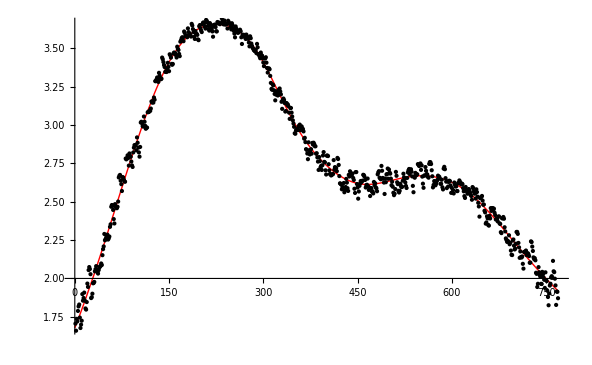

```mathematica
Plot[nlm[x],{x,0,770},Epilog:>Point[data],PlotStyle->{Red,Thick}]
```

```mathematica
nlm["RSquared"]
```

0.999101